```mathematica
ClearAll["Global`*"]
```

(0 | 1
-1 | 0)

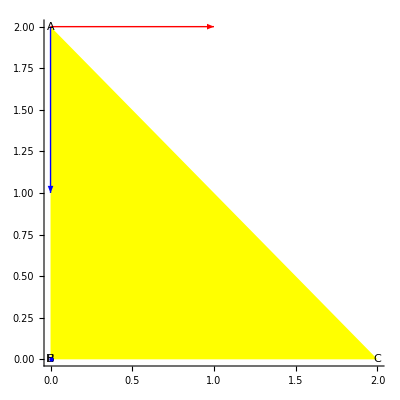

```mathematica
L=2;
ra={0,L};
rb={0,0};
rc={L,0};
AB=rb-ra;
AC=rc-ra;
AB0=AB/Norm@AB;
xx=AB0;
AC0=AC/Norm@AC;
AH=AB0*AB0.AC;
HC=AC-AH;
yy=HC/Norm@HC;
A=Transpose[{xx,yy}]; (*составляем матрицу преобразования из ортов новых в старом базисе*)
A//MatrixForm

{Show[Graphics[{{Yellow,Triangle[{ra,rb,rc}]},{Blue,Arrow[{ra,ra+xx}]},{Red,Arrow[{ra,ra+yy}]},Text["B",rb,Background->White],Text["C",rc,Background->White],Text["A",ra,Background->White],Text["H",ra+AH,Background->White],{Blue,Point[ra+AH]}},Axes->True]]}
```

```mathematica
I1=Integrate[E^(I (ξxx xprime+ξyy yprime)),{xprime,0,nAH},{yprime,0,xprime*nHC/nAH}];
```

```mathematica
I2=Integrate[E^(I (ξxx xprime+ξyy yprime)),{xprime,nAH,nAH+nHB},{yprime,0,nHC*(1- (xprime - nAH)/nHB)}];
```

```mathematica
FullSimplify[I1+I2]
```

(nHC (-nHB ξxx+ⅇ^(ⅈ (nAH ξxx+nHC ξyy)) (nAH+nHB) ξxx+nHC ξyy-ⅇ^(ⅈ (nAH+nHB) ξxx) (nAH ξxx+nHC ξyy)))/(ξxx (nHB ξxx-nHC ξyy) (nAH ξxx+nHC ξyy))

```mathematica
FF[ξxx_,ξyy_,nAH_,nHC_,nHB_]:=(nHC (-nHB ξxx+ⅇ^(ⅈ (nAH ξxx+nHC ξyy)) (nAH+nHB) ξxx+nHC ξyy-ⅇ^(ⅈ (nAH+nHB) ξxx) (nAH ξxx+nHC ξyy)))/(ξxx (nHB ξxx-nHC ξyy) (nAH ξxx+nHC ξyy))
```

```mathematica
Limit[Limit[FF[ξxx,ξyy,nAH,nHC,nHB],{ξxx->0}],{ξyy->0}]
```

{2}

```mathematica
FlyingTriangle2D[ra_,rb_,rc_,kx_,ky_]:={
AB=rb-ra;
AC=rc-ra;
AB0=AB/Norm@AB;
xx=AB0;
AC0=AC/Norm@AC;
AH=AB0*AB0.AC;
HC=AC-AH;
yy=HC/Norm@HC;
A={xx,yy};
ξ=A.{kx,ky};
nAH=Norm@AH;
nHC=Norm@HC;
nHB=Norm@(AB-AH);
ξxx=ξ[[1]];
ξyy=ξ[[2]];
FullSimplify[E^(I{kx,ky}.ra)FF[ξxx,ξyy,nAH,nHC,nHB]]
}[[1]]
```

```mathematica
SpectralTriangle= FlyingTriangle2D[ra,rb,rc,kx,ky];
{FullSimplify[ SpectralTriangle-Tri1 ],FullSimplify[ SpectralTriangle-Tri2 ],FullSimplify[ SpectralTriangle-Tri3] }
```

{0,(4 (ky Cos[ky] Sin[kx]-kx Cos[kx] Sin[ky]) (-ⅈ Cos[kx+ky]+Sin[kx+ky]))/((kx-ky) ky (kx+ky)),(4 (ky Cos[ky] Sin[kx]-kx Cos[kx] Sin[ky]) (-ⅈ Cos[kx+ky]+Sin[kx+ky]))/(kx (kx-ky) (kx+ky))}

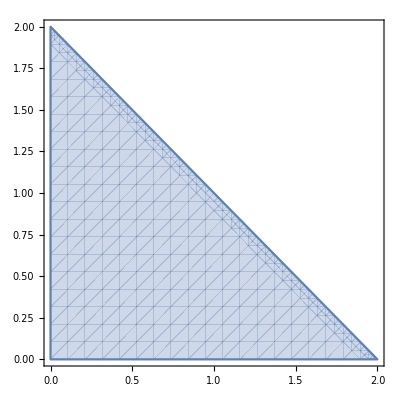
{((-1+ⅇ^(2 ⅈ ky)) kx+ky-ⅇ^(2 ⅈ kx) ky)/(kx (kx-ky) ky),-Graphics-}

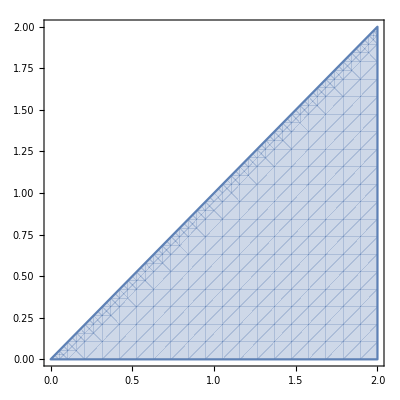
{(-ky+ⅇ^(2 ⅈ kx) (kx-ⅇ^(2 ⅈ ky) kx+ky))/(kx ky (kx+ky)),-Graphics-}

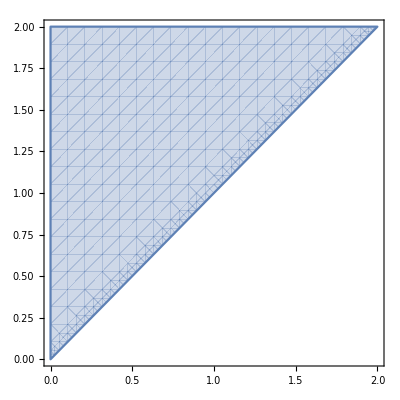
{(-kx+ⅇ^(2 ⅈ ky) (kx+ky-ⅇ^(2 ⅈ kx) ky))/(kx ky (kx+ky)),-Graphics-}

```mathematica
{Tri1=FullSimplify@Integrate[E^(I (kx x+ky y)),{x,0,L},{y,0,L-x}],RegionPlot[x+y<L,{x,0,L},{y,0,L}]}
{Tri2=FullSimplify@Integrate[E^(I (kx x+ky y)),{x,0,L},{y,0,x}],RegionPlot[y<x,{x,0,L},{y,0,L}]}
{Tri3=FullSimplify@Integrate[E^(I (kx x+ky y)),{x,0,L},{y,x,L}],RegionPlot[y>x,{x,0,L},{y,0,L}]}
```

```mathematica
p=2;
maxp=10;
k0=(2π)/L;
 FieldInduced[xrec_,yrec_]:=SetPrecision[NIntegrate[SetPrecision[N@HankelH1[0,k0*√((xrec-x)^2+(yrec-y)^2)],maxp],{x,0,L},{y,0,x},PrecisionGoal->p,WorkingPrecision->maxp],p];
Timing@FieldInduced[10*L,0]
```

{0.0156001,0.05+0.054 ⅈ}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

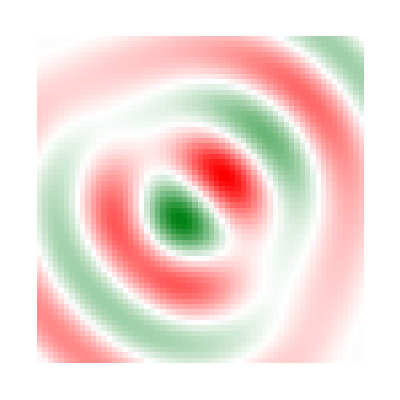

```mathematica
Nplot=60;
FIELD=ParallelTable[FieldInduced[3*L*(i/Nplot-1/3),3*L*(j/Nplot-1/3)],{i,0,Nplot},{j,0,Nplot}];ArrayPlot[Re@FIELD,ColorFunction-> ColorData["RedGreenSplit"]]
```

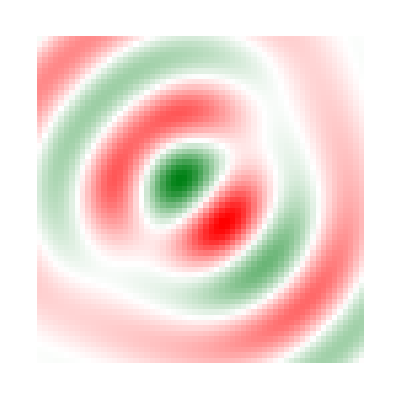

```mathematica
(*truncated spectral representation*)
GLk [s_,L_,k0_]:=(1+(I π)/2 L s BesselJ[1,L s] HankelH1[0,L k0])/(s^2-k0^2)-((I π)/2 L k0 BesselJ[0,L s]HankelH1[1,L k0])/(s^2-k0^2)
```

```mathematica
f2=ParallelTable[i+j,{i,0,10},{j,0,10}]
```

{{0,1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{2,3,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12,13},{4,5,6,7,8,9,10,11,12,13,14},{5,6,7,8,9,10,11,12,13,14,15},{6,7,8,9,10,11,12,13,14,15,16},{7,8,9,10,11,12,13,14,15,16,17},{8,9,10,11,12,13,14,15,16,17,18},{9,10,11,12,13,14,15,16,17,18,19},{10,11,12,13,14,15,16,17,18,19,20}}

```mathematica
ArrayPlot[Re@f2,ColorFunction->GrayLevel]
```

-Graphics-